### Intersección con círculo:

```mathematica
r=1.5;
EspacioFase={};
Inc[{p_,d_}]:=
Module[
{eqs=(p-{0,0}+t d).(p-{0,0}+t d)-r^2,sol},
sol=Select[t/.Solve[eqs==0,t],(Im[#]==0&&#>0)&];
Return[{If[sol==={},{},p+t d/.t->Min[sol]],d}];
];
```

#### Ángulos de sálida

```mathematica
Angc[{s_,d_}]:= Module[{n,θ,α },
n = s/(√(s.s));

α = Apply[ArcTan,n];
θ = ArcCos[d.n];
AppendTo[EspacioFase,{α,θ}];

Return[{s, d-2d.n *n}];
];
```

#### Choque con círculo

```mathematica
ChoqueCirculo[{p_,d_}]:=Module[{s},
s = Inc[{p,d}];
Return[
If[First[s] == {},
{},
Angc[s]
]
];
];
```

### Intersección con paredes

```mathematica
Inp[{p_,d_}]:=
Module[
{A=Flatten[{Solve[First[(p+d t)]==2,t],Solve[Last[(p+d t)]==2,t],Solve[First[(p+d t)]==-2,t],Solve[Last[(p+d t)]==-2,t]},1],solu}, solu=Select[t/.A,(Im[#]==0&&#>0)&];
Return[{If[solu==={},{},icp=p+t d/.t->Min[solu]],d}];
];
```

#### Ángulo de reflexión con pared

```mathematica
Angp[{s_,d_}]:= Module[{rules},
rules = {
{_?(#<-1.9999&),_}:>{-First[d],Last[d]},
{_?(#>1.9999&),_}:>{-First[d],Last[d]},
{_,_?(#<-1.9999&)}:>{First[d],-Last[d]},
{_,_?(#>1.9999 &)}:>{First[d],-Last[d]}
};
Return[{s,Replace[s,rules]}];
];
```

#### Choque con pared

```mathematica
ChoquePared[{p_,d_}]:= Angp[Inp[{p,d}]];
```

### Inicializar

```mathematica
CHOQUEPARED = 1;
CHOQUEQUIENSABE = 2;
Choque[{{p_,d_},tipo_}]:=Module[{ChoqueeCirculo},
If[tipo == CHOQUEPARED,
Return[{ChoquePared[{p,d}],CHOQUEQUIENSABE}];
,

ChoqueeCirculo = ChoqueCirculo[{p,d}];
If[Length[ChoqueeCirculo]>0,
Return[{ChoqueeCirculo,CHOQUEPARED}];,
Return[{ChoquePared[{p,d}],CHOQUEQUIENSABE}];
];
]
];
```

### Resultados

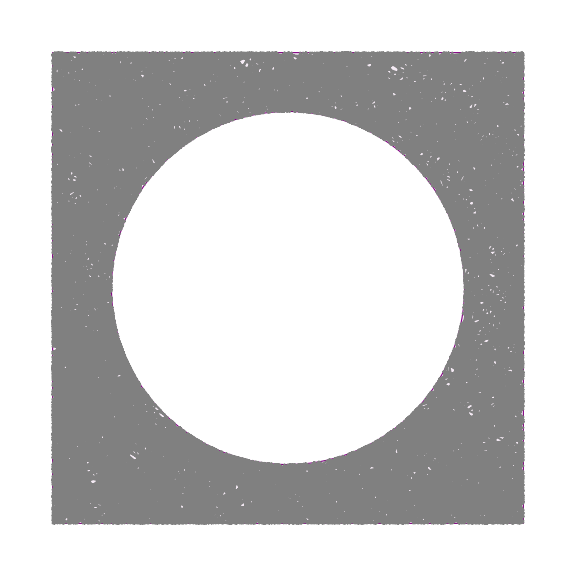

```mathematica
EspacioFase = {};
Resultados = NestList[Choque,{{{0,r},{Cos[.8],Sin[.8]}},CHOQUEPARED},2000];
EspacioFase;
Trayectoria=ListLinePlot[Style[Resultados[[All,1,1]],Gray] ];
Graf=Graphics[{{{Lighter[LightPurple],EdgeForm[{Thick,Purple}],Rectangle[{-2,-2},{2,2}],White,Disk[{0,0},{r,r}]} }},ImageSize->Large];
Show[Graf,Trayectoria]
```

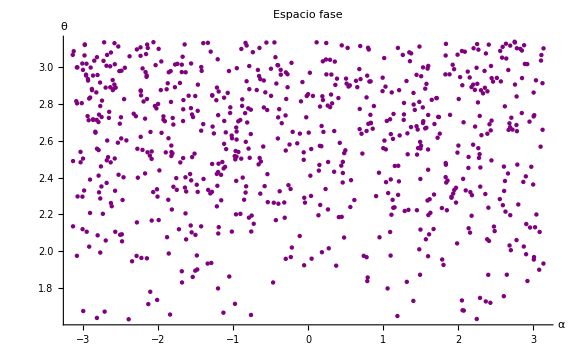

```mathematica
ListPlot[Style[EspacioFase, Purple], PlotLabel->"Espacio fase", AxesLabel->{"α","θ"},ImageSize->Large]
```